```mathematica
text=Import["/mnt/4T/last/zhc/Documents/ncm/new/extracted.csv"]
```

```mathematica
data=#[[6]]/1000/60&/@text[[2;;]]//N;
```

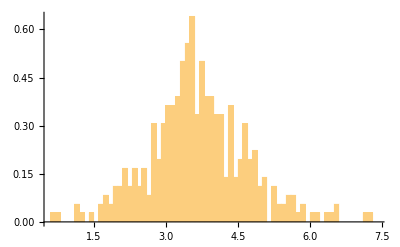

```mathematica
Histogram[data,200,"PDF"]
```

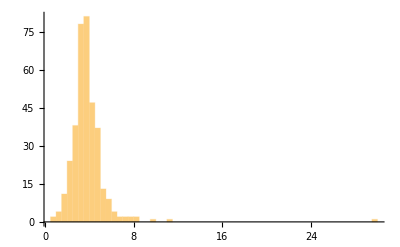

```mathematica
Histogram[data,PlotRange->All]
```